```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=If[s==0,-2Log[m],If[s==4 m^2,2-2Log[m],2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]]] ;
ScalarFPrime0[m_,s_]:=If[s==4 m^2,-1/(4 m^2),-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))ArcTan[(√s)/(√(4 m^2-s))]];
PropagatorScalar[s_,M_,m_,c_,Γ_]:=1/(s-M^2+ⅈ×M×Γ+c×(Re[ScalarF0[m,s]-ScalarF0[m,M^2]]-(s-M^2)Re[ScalarFPrime0[m,M^2]]));
```

```mathematica
NWA[p_,A_,B_,C_]:=C/((p^2-A)^2+B);
```

```mathematica
BestFit[m_,c_,Γ_]:=NMinimize[{Sum[(Abs[PropagatorScalar[p^2,1,m,c,Γ]]^2-NWA[p,A,B,C])^2,{p,0,2,0.01}],A>0,B>0,C>0},{A,B,C},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->MachinePrecision];
```

```mathematica
Res1=BestFit[0.49,0.15,0.1]
```

{1858.43,{A→1.0159,B→0.00509135,C→0.530087}}

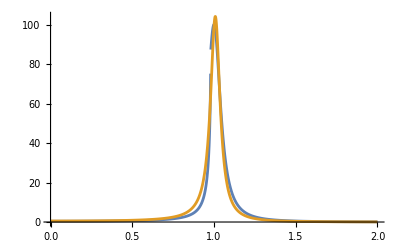

```mathematica
Plot[{Abs[PropagatorScalar[p^2,1,0.49,0.15,0.1]]^2,NWA[p,A,B,C]/.Res1[[2]]},{p,0,2},PlotRange->All]
```